Levin with approximation

2.07666×10^-18 √((3.57907×10^-26 f^2-(3.07918×10^-28 f^(3/2) (-Sin[348.703 √f]+Sinh[348.703 √f]))/(-Cos[348.703 √f]+Cosh[348.703 √f]))/((-0.000626657 √(f^2) Cos[0.00021933 √(f^2)]+0.000279798 f^2 Sin[0.00021933 √(f^2)])^2))

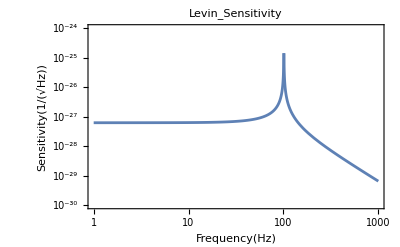

```mathematica
LevinPS=(4 kB T^2 α^2)/κ(1/((M ω^2)/(s E0)Sin[k2 L]-k2 Cos[k2 L]))^2(L^3/3(k2/kd)^4-L^2/2 k2^4/kd^5(Sinh[2 kd L]-Sin[2 kd L])/(Cosh[2 kd L]-Cos[2 kd L]))/.
{k2->√((ρ ω^2)/(s E0)),kd->√(ω/(2χ)),χ->κ/(ρ Cv)}/.
{kB->1.38 10^-23,T->300,α->5.0*10^(-6),L->0.35,κ->0.00008,ρ->0.008,Cv->7.9 10^2,ω->2π f,E0->4.0*10^(11),M->22.8/4,s->0.0016^2 Pi/4,χ->1.266*10^-5};
LevinSensi=Sqrt[LevinPS] / 200 / 3000
LevinSensiG=LogLogPlot[LevinSensi,{f,1,1000},PlotRange->{{1,1000},{10^-30,10^-24}},PlotLabel->Levin_Sensitivity,Frame->True,FrameLabel->{Frequency[Hz],Sensitivity[1/Sqrt[Hz]]}]
```

Levin without approximation

```mathematica
LevinPSwoApp=
```